```mathematica
Get[FileNameJoin[{NotebookDirectory[],"ksp_system_convergence.generated.wl"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"solar_system_convergence.generated.wl"}]]
```

```mathematica
getTime[ppaConvergence_]:=Map[{#⟦4⟧,#⟦2⟧}&,ppaConvergence]
```

```mathematica
getStep[ppaConvergence_]:=Map[{#⟦1⟧,#⟦2⟧}&,ppaConvergence]
```

```mathematica
blanesSolarSystemConvergence=ppaSolarSystemConvergence0
```

{{128. s,1.09723 m,Mimas,49.6855 s},{256. s,3.6432 m,Phobos,25.062 s},{512. s,10.8236 m,Phobos,12.218 s},{1024. s,396.299 m,Phobos,6.044 s},{2048. s,25183. m,Phobos,3.0675 s},{4096. s,2.58644×10^6 m,Phobos,1.526 s},{8192. s,4.52282×10^7 m,Phobos,0.769 s}}

```mathematica
mclachlanSolarSystemConvergence=ppaSolarSystemConvergence1
```

{{64. s,0.798728 m,Miranda,53.3992 s},{128. s,2.54315 m,Mimas,26.6773 s},{256. s,31.0356 m,Phobos,13.2817 s},{512. s,1972.48 m,Phobos,6.69734 s},{1024. s,121533. m,Phobos,3.34967 s},{2048. s,6.70313×10^6 m,Phobos,1.67834 s},{4096. s,1.85864×10^7 m,Phobos,0.843169 s}}

```mathematica
quinlan8SolarSystemConvergence=ppaSolarSystemConvergence2
```

{{128. s,2.27953 m,Mimas,8.13413 s},{256. s,2.15535 m,Phobos,4.08732 s},{512. s,762.803 m,Phobos,2.07241 s},{1024. s,210602. m,Phobos,1.06471 s},{2048. s,1.59886×10^7 m,Phobos,0.564613 s}}

```mathematica
quinlan10SolarSystemConvergence=ppaSolarSystemConvergence3
```

{{128. s,2.25676 m,Phobos,8.64623 s},{256. s,4.12555 m,Mimas,4.35387 s},{512. s,1.28519×10^7 m,Phobos,2.19644 s},{1024. s,5.92109×10^11 m,Phobos,1.14773 s},{2048. s,2.06059×10^12 m,Mimas,0.632126 s}}

```mathematica
quinlan12SolarSystemConvergence=ppaSolarSystemConvergence4
```

{{128. s,4.16685 m,Phobos,9.20934 s},{256. s,4.9409 m,Phobos,4.63143 s},{512. s,2.32151 m,Mimas,2.34447 s},{1024. s,3.84679×10^11 m,Phobos,1.22024 s},{2048. s,2.51582×10^11 m,Phobos,0.628626 s}}

```mathematica
preferredSolarSystemConvergence=ppaSolarSystemConvergence5
```

{{150. s,0.902438 m,Miranda,7.82406 s},{300. s,0.542687 m,Io,3.96879 s},{600. s,2.29845 m,Miranda,2.0164 s},{1200. s,3.59119×10^10 m,Phobos,1.02971 s}}

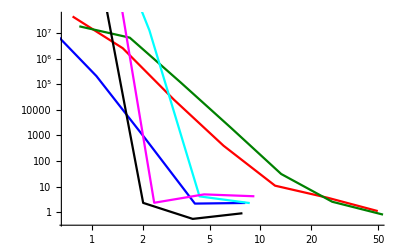

```mathematica
Show[
ListLogLogPlot[getTime[blanesSolarSystemConvergence], Joined->True,PlotStyle->RGBColor["red"]],
ListLogLogPlot[getTime[mclachlanSolarSystemConvergence], Joined->True,PlotStyle->RGBColor["green"]],
ListLogLogPlot[getTime[quinlan8SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["blue"]],
ListLogLogPlot[getTime[quinlan10SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["cyan"]],
ListLogLogPlot[getTime[quinlan12SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["magenta"]],
ListLogLogPlot[getTime[preferredSolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["black"]]
]
```

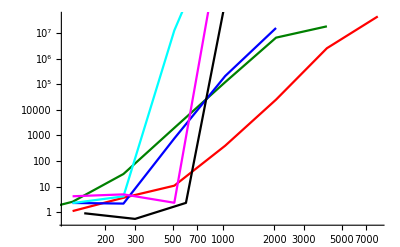

```mathematica
Show[
ListLogLogPlot[getStep[blanesSolarSystemConvergence], Joined->True,PlotStyle->RGBColor["red"]],
ListLogLogPlot[getStep[mclachlanSolarSystemConvergence], Joined->True,PlotStyle->RGBColor["green"]],
ListLogLogPlot[getStep[quinlan8SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["blue"]],
ListLogLogPlot[getStep[quinlan10SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["cyan"]],
ListLogLogPlot[getStep[quinlan12SolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["magenta"]],
ListLogLogPlot[getStep[preferredSolarSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["black"]]
]
```

```mathematica
blanesKSPSystemConvergence=ppaKSPSystemConvergence0
```

{{128. s,0.0916492 m,Laythe,8.337 s},{256. s,0.292926 m,Laythe,4.1965 s},{512. s,0.143869 m,Laythe,2.0855 s},{1024. s,11.443 m,Laythe,1.06 s},{2048. s,719.806 m,Laythe,0.533 s},{4096. s,45807.7 m,Laythe,0.284 s},{8192. s,8.13076×10^7 m,Laythe,0.1505 s}}

```mathematica
mclachlanKSPSystemConvergence=ppaKSPSystemConvergence1
```

{{64. s,0.0692022 m,Laythe,9.5855 s},{128. s,0.0890168 m,Laythe,4.7915 s},{256. s,1.05871 m,Laythe,2.4195 s},{512. s,57.8538 m,Laythe,1.2165 s},{1024. s,3631.42 m,Laythe,0.622 s},{2048. s,223505. m,Laythe,0.331 s},{4096. s,1.21951×10^7 m,Laythe,0.165 s}}

```mathematica
quinlan8KSPSystemConvergence=ppaKSPSystemConvergence2
```

{{128. s,0.0530015 m,Vall,2.6525 s},{256. s,0.173594 m,Laythe,1.34 s},{512. s,8.96451 m,Bop,0.6805 s},{1024. s,7526.03 m,Bop,0.3595 s},{2048. s,3.76326×10^6 m,Gilly,0.1945 s}}

```mathematica
quinlan10KSPSystemConvergence=ppaKSPSystemConvergence3
```

{{128. s,0.0391452 m,Laythe,2.888 s},{256. s,0.0910918 m,Laythe,1.4685 s},{512. s,0.321321 m,Bop,0.7495 s},{1024. s,1135.55 m,Bop,0.3965 s},{2048. s,2.5202×10^11 m,Laythe,0.232 s}}

```mathematica
quinlan12KSPSystemConvergence=ppaKSPSystemConvergence4
```

{{128. s,0.0418977 m,Laythe,3.137 s},{256. s,0.0409186 m,Laythe,1.5905 s},{512. s,0.945253 m,Bop,0.8205 s},{1024. s,2575.11 m,Gilly,0.436 s},{2048. s,1.84901×10^11 m,Laythe,0.211 s}}

```mathematica
preferredKSPSystemConvergence=ppaKSPSystemConvergence5
```

{{150. s,0.201244 m,Laythe,2.7385 s},{300. s,0.121402 m,Laythe,1.376 s},{600. s,28.0249 m,Bop,0.718 s},{1200. s,26519. m,Bop,0.381 s}}

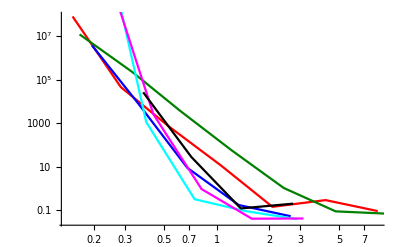

```mathematica
Show[
ListLogLogPlot[getTime[blanesKSPSystemConvergence], Joined->True,PlotStyle->RGBColor["red"]],
ListLogLogPlot[getTime[mclachlanKSPSystemConvergence], Joined->True,PlotStyle->RGBColor["green"]],
ListLogLogPlot[getTime[quinlan8KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["blue"]],
ListLogLogPlot[getTime[quinlan10KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["cyan"]],
ListLogLogPlot[getTime[quinlan12KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["magenta"]],
ListLogLogPlot[getTime[preferredKSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["black"]]
]
```

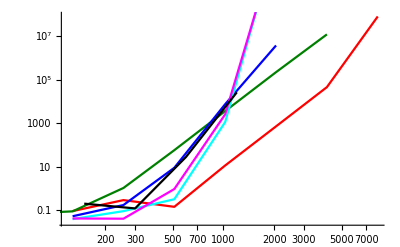

```mathematica
Show[
ListLogLogPlot[getStep[blanesKSPSystemConvergence], Joined->True,PlotStyle->RGBColor["red"]],
ListLogLogPlot[getStep[mclachlanKSPSystemConvergence], Joined->True,PlotStyle->RGBColor["green"]],
ListLogLogPlot[getStep[quinlan8KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["blue"]],
ListLogLogPlot[getStep[quinlan10KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["cyan"]],
ListLogLogPlot[getStep[quinlan12KSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["magenta"]],
ListLogLogPlot[getStep[preferredKSPSystemConvergence], Joined->True,PlotRange->All,PlotStyle->RGBColor["black"]]
]
```